```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/chi-q_dist/num"]
```

/Users/yuichirotada/Documents/Univ/chi-q_dist/num

```mathematica
$Assumptions={β>0,KK>0,Mk0>0,M>0,calM>0,q>0,a2>0,M1>0,M2>0};
```

```mathematica
xpcoord={a1,a2,ν1,ν2,c1,c2,ϕ1,ϕ2};
n=8;
```

```mathematica
MPBH[ν_]=KK Mk0(ν σ0-νth σ0)^β;
νPBH[M_]=(M/(KK Mk0))^(1/β)/σ0+νth;
```

```mathematica
MPBH[νPBH[M]]//Simplify
```

M

```mathematica
xcoordinxp={a1,a2,MPBH[ν1],MPBH[ν2],c1,c2,ϕ1,ϕ2};
Jxxp=Table[D[xcoordinxp[[j]], xpcoord[[i]]],{i,n},{j,n}]//Simplify
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,KK Mk0 β σ0 ((ν1-νth) σ0)^(-1+β),0,0,0,0,0},{0,0,0,KK Mk0 β σ0 ((ν2-νth) σ0)^(-1+β),0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Det[Jxxp]//Simplify
Det[Jxxp]/.{ν1->νPBH[M1],ν2->νPBH[M2]}//Simplify
```

KK^2 Mk0^2 β^2 σ0^2 ((ν1-νth) σ0)^(-1+β) ((ν2-νth) σ0)^(-1+β)

(M1^(1/β))^(-1+β) (M2^(1/β))^(-1+β) (KK Mk0)^(2/β) β^2 σ0^2

```mathematica
charpM[M1_,M2_]=(M1 M2)^(3/5)/(M1+M2)^(1/5);
ratioq[M1_,M2_]=M2/M1;
χeff[a1_,a2_,q_,c1_,c2_]=(a1 c1+q a2 c2)/(1+q);
M1Mq[calM_,q_]=M1/.Solve[charpM[M1,M2]==calM&&ratioq[M1,M2]==q,{M1,M2}][[1]]
M2Mq[calM_,q_]=M2/.Solve[charpM[M1,M2]==calM&&ratioq[M1,M2]==q,{M1,M2}][[1]]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

(calM (1+q)^(1/5))/q^(3/5)

Solve::nongen: Solutions may not be valid for all values of parameters.

calM q^(2/5) (1+q)^(1/5)

```mathematica
charpM[M1Mq[calM,q],M2Mq[calM,q]]//Simplify
ratioq[M1Mq[calM,q],M2Mq[calM,q]]//Simplify
```

calM

q

```mathematica
xcoord={a1,a2,M1,M2,c1,c2,ϕ1,ϕ2};
zcoord={Log[charpM[M1,M2]],ratioq[M1,M2],χeff[a1,a2,ratioq[M1,M2],c1,c2],a1,a2,c1,ϕ1,ϕ2}
```

{Log[(M1 M2)^(3/5)/(M1+M2)^(1/5)],M2/M1,(a1 c1+(a2 c2 M2)/M1)/(1+M2/M1),a1,a2,c1,ϕ1,ϕ2}

```mathematica
Jzx=Table[D[zcoord[[j]], xcoord[[i]]],{i,n},{j,n}]//Simplify
```

{{0,0,(c1 M1)/(M1+M2),1,0,0,0,0},{0,0,(c2 M2)/(M1+M2),0,1,0,0,0},{(2 M1+3 M2)/(5 M1^2+5 M1 M2),-M2/M1^2,((a1 c1-a2 c2) M2)/(M1+M2)^2,0,0,0,0,0},{(3 M1+2 M2)/(5 M1 M2+5 M2^2),1/M1,(-a1 c1 M1+a2 c2 M1)/(M1+M2)^2,0,0,0,0,0},{0,0,(a1 M1)/(M1+M2),0,0,1,0,0},{0,0,(a2 M2)/(M1+M2),0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

```mathematica
Det[Jzx]//Simplify
Det[Jzx]/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
```

-(a2 M2)/(M1^2 (M1+M2))

-(a2 q^(11/5))/(calM^2 (1+q)^(7/5))

```mathematica
1/(Det[Jxxp]Abs[Det[Jzx]])/.{ν1->νPBH[M1],ν2->νPBH[M2]}/.{M1->M1Mq[calM,q],M2->M2Mq[calM,q]}//Simplify
```

(((calM^2 (1+q)^(2/5))/(KK^2 Mk0^2 q^(1/5)))^(1/β) (1+q))/(a2 q^2 β^2 σ0^2)

```mathematica
νth=8;
KK=3.3;
β=0.36;
γ=0.85;
```

```mathematica
δbH=0.768;
νbth=2/5 νth;
σH=δbH/νbth
```

0.24

```mathematica
Ph[h_]=563 h^2 Exp[−12h+2.5 h^1.5+8−3.2(1500+h^16)^(1/8)];
Cν[ν_]=1.56 10^-3 Sqrt[1-γ^2] KK^(-1/3)σH^(-β/3)(ν-νth)^(-1/3)((2/5 ν)/8)^-2;
```

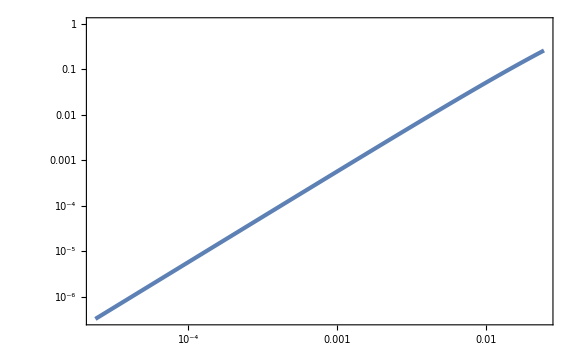

```mathematica
LogLogPlot[Ph[h],{h,0,Cν[8.000000000001]^-1}]
```

```mathematica
Na[ν_]:=NIntegrate[Ph[h],{h,0,Cν[ν]^-1}]
```

```mathematica
NaList=Table[{νth+10^dlogν,Na[νth+10^dlogν]},{dlogν,-10,1,1/100}];//AbsoluteTiming
```

{3.49228,Null}

```mathematica
Naint[ν_]=Interpolation[NaList][ν];
```

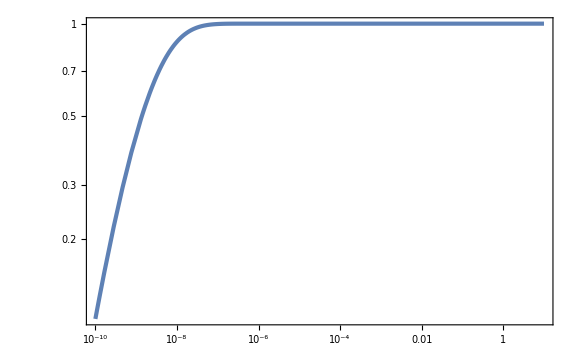

```mathematica
LogLogPlot[Naint[νth+δν],{δν,10^-10,10},PlotRange->Full]
```

```mathematica
Pa[a_,ν_]=(Cν[ν]^-1 Ph[Cν[ν]^-1 a])/Naint[ν];
```

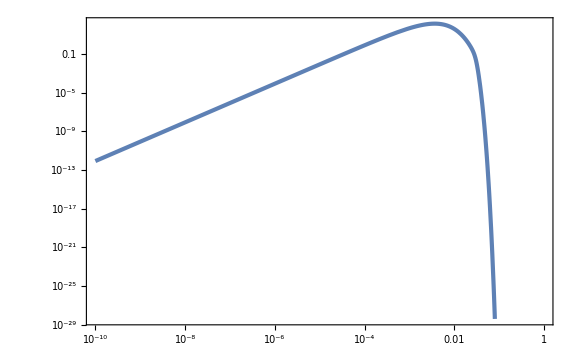

```mathematica
LogLogPlot[Pa[a,νth+10^-2],{a,10^-10,1}]
```

```mathematica
NIntegrate[Pa[a,νth+10^1],{a,0,1}]
```

1.

```mathematica
LL[a1_,a2_,χ_,q_]=Min[1,((1+q)χ+q a2)/a1]-Max[-1,((1+q)χ-q a2)/a1];
Pν[ν_]=Sqrt[2/π] Erfc[νth/Sqrt[2]]^-1 Exp[-ν^2/2];
ν2[ν1_,q_]=q^(1/β)(ν1-νth)+νth;
```

```mathematica
ν2[νth+10,0]
```

8.

```mathematica
Clear[Pintegrand]
```

```mathematica
Pintegrand[χ_,q_,log10a1_,log10a2_,log10δν1_]:=LL[10^log10a1,10^log10a2,χ,q] Log[10]^3 10^(log10a1+2log10δν1)Pa[10^log10a1,νth+10^log10δν1]Pν[νth+10^log10δν1]Pa[10^log10a2,ν2[νth+10^log10δν1,q]]Pν[ν2[νth+10^log10δν1,q]]/;LL[10^log10a1,10^log10a2,χ,q]>0
Pintegrand[χ_,q_,log10a1_,log10a2_,log10δν1_]:=0/;!(LL[10^log10a1,10^log10a2,χ,q]>0)
```

```mathematica
Pintegrand[0,1,-5,-5,-5]
```

1.12002×10^-22

```mathematica
Pχq[χ_,q_]:=NIntegrate[Pintegrand[χ,q,log10a1,log10a2,log10δν1],{log10a1,-7,0},{log10a2,-7,0},{log10δν1,-7,1},Method->"AdaptiveMonteCarlo"]
```

```mathematica
Pχq[0,1]//AbsoluteTiming
```

{1.40455,179.979}

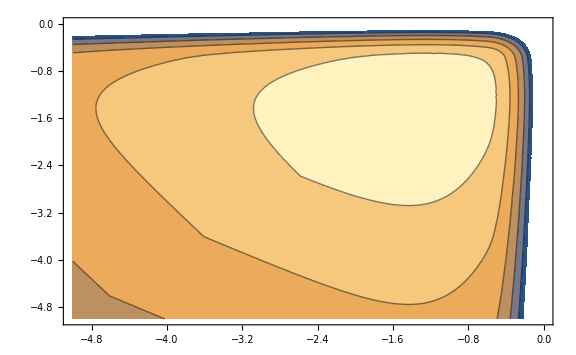

```mathematica
ContourPlot[Log10[Pintegrand[0,1,log10a1,log10a2,-5]],{log10a1,-5,0},{log10a2,-5,0}]
```

```mathematica
P0qList=ParallelTable[{i/10,Pχq[0,i/10]//Quiet},{i,1,10}];//AbsoluteTiming
```

{31.0494,Null}

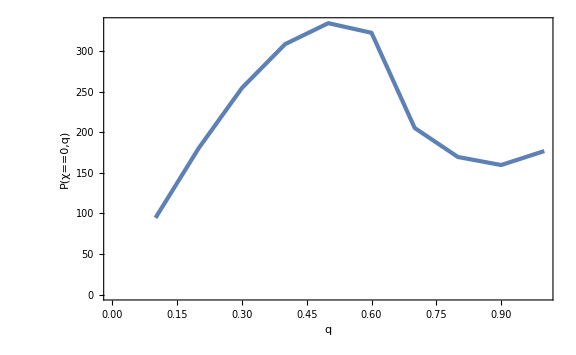

```mathematica
ListPlot[P0qList,FrameLabel->{q,P[χ==0,q]}]
```

```mathematica
PχqList=Flatten[ParallelTable[{logχ,q,Log10[Pχq[10^logχ,q]//Quiet]},{logχ,-7,0,1/50},{q,0,1,1/50}],1];//AbsoluteTiming
```

{56630.4,Null}

```mathematica
Export["Pchiq.dat",PχqList];
```

```mathematica
2363 25/86400//N
```

0.683738

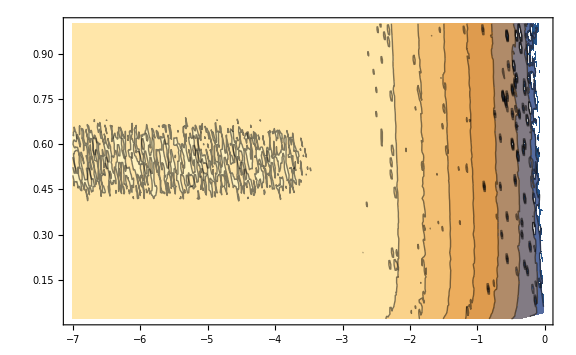

```mathematica
ListContourPlot[PχqList]
```

```mathematica
Pχqint[χ_,q_]=10^(Interpolation[PχqList,InterpolationOrder->1][Log10[χ],q]);
```

```mathematica
FigPχqContour=ContourPlot[Log10[Log[10] 10^logχ Pχqint[10^logχ,q]],{logχ,-7,0},{q,0,1},Contours->Table[i,{i,-15,0}],FrameLabel->{"log_10"χ,q},PlotLegends->BarLegend[Automatic,LegendLabel->Placed["log_10"P["log_10"χ,q],Right,Rotate[#,-90Degree]&]]]
```

-Graphics-

```mathematica
Export["PchiqContour.pdf",FigPχqContour];
```

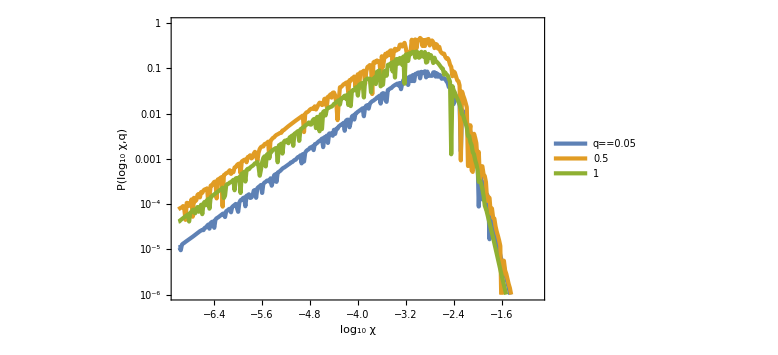

```mathematica
LogPlot[{Log[10] 10^logχ Pχqint[10^logχ,0.05],Log[10] 10^logχ Pχqint[10^logχ,0.5],Log[10] 10^logχ Pχqint[10^logχ,1]},{logχ,-7,-1},PlotRange->{10^-6,1},FrameLabel->{"log_10"χ,P["log_10"χ,q]},PlotLegends->Placed[LineLegend[{q==0.05,0.5,1},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"],LegendLayout->"Row"],{0.4,0.15}]]
```

```mathematica
NIntegrate[Log[10] 10^logχ Pχqint[10^logχ,q],{logχ,-7,0},{q,1/50,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.305851+5.39397×10^-17 ⅈ and 0.000034758 for the integral and error estimates.

0.305851